# Risanje in reševanje enačb z Mathematico

Vaje v tem zvezku pogosto vsebujejo povezavo na dokumentacijo funkcije, ki jo morate uporabiti. Priporočamo, da dokumentacijo vsaj preletite. Včasih navodila omenijo dodatne nastavitve, tudi te poiščite v dokumentaciji.

Spodnja dva primera ilustrirata obe vrsti prirejanja.

```mathematica
(* Takojšnje prirejanje *) (* Vrednost izraza na desni se izračuna in shrani v spremenljivko na desni. Vrednost v spremenljivki ostane enaka. *)
f1=RandomInteger[{0,10}];
f1
f1
f1
```

```mathematica
(* Zakasnjeno prirejanje *)
(* V spremenljivko se shrani izraz na desni, njegova vrednost pa se izračuna vsakič, ko pogledamo, kakšna vrednost je v spremenljivki. *)
f2:=RandomInteger[{0,10}];
f2
f2
f2
```

## Funkcije in njihovi grafi

### Subsection. naloga:

1. Definirajte funkcijo f spremenljivke x s funkcijskim predpisom (x^2-1)/(x^2-4).
2. S funkcijo Plot narišite njen graf na intervalu [-5,5]. Označite še njene pole, tako da dodate nastavitev ExclusionsStyle→{{Dashed,Red}}
3. S funkcijo Solve poiščite ničle in pole funkcije f. Pri polih vam bo prišla prav še funkcija Denominator.
4. Izračunajte levo limito enega izmed polov (funkciji Limit dodate še nastavitev Direction→1).
5. Izračunajte limito funkcije, ko gre .
6. Določite stacionarne točke.
7. S funkcijo Reduce določite intervale konveksnosti (ko velja )
Za vajo lahko doma na podoben način analizirate tudi funkcijo g(x)=arctg x^2/(x^2-1).

```mathematica
f[x_]:=(x^2-1)/(x^2-4)
```

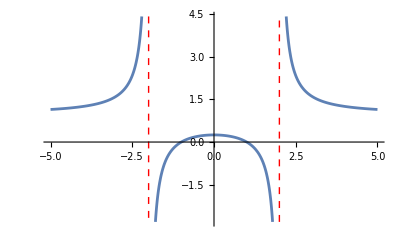

```mathematica
Plot[f[x],{x,-5,5},ExclusionsStyle->{{Dashed, Red}}]
```

```mathematica
x/.Solve[f[x]==0,x]
```

{-1,1}

```mathematica
x/.Solve[Denominator[f[x]] == 0,x]
```

{-2,2}

```mathematica
Limit[f[x],x->-2, Direction->1]
```

∞

```mathematica
Limit[f[x],x->Infinity]
```

1

```mathematica
x/.Solve[D[f[x]==0,x]]
```

{0}

```mathematica
Reduce[f''[x]>0]
```

x<-2||x>2

### Subsection. naloga:

1. Dana je parametrično podana krivulja (((3-t) sin t)/(t+1),cos (t) sin (2t)). Definirajte jo kot funkcijo ene spremenljivke.
2. Narišite krivuljo k za  t∈[0,5] s pomočjo funkcije ParametricPlot.
3. Krivulja seče samo sebe natanko dvakrat. S pomočjo numeričnega reševanja enačb (FindRoot) poišči približek presečišč. Enačbo nastavi tako da izenačiš krivuljo, parametrizirano s parametrom t, s krivuljo, parametrizirano s parametrom s. Potem s spreminjanjem začetnih približkov parametrov t in s poskusi določiti vrednosti parametrov, pri katerih pride do samopresečič (dovolj bodo celoštevilske vrednosti, od katerih bo ena enaka 0).

```mathematica
k[t_]:={((3-t)*Sin[t])/(t+1), Cos[t]*Sin[2t]}
```

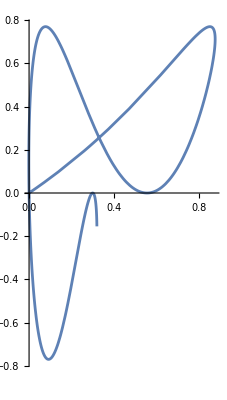

FindRoot::nlnum: The function value {0.+((3.-1. t) Sin[t])/(1.+t),Cos[t] Sin[2. t]} is not a list of numbers with dimensions {2} at {s} = {0.}.

```mathematica
ParametricPlot[k[t],{t,0,5}]
```

```mathematica
resiev1=FindRoot[k[t]==k[s],{t,0},{s,2}]
```

```mathematica
{t->0.13041607259050386,s->1.9509318447573987}
resitev2= FindRoot[k[t]==k[s],{t,0},{s,3}]
```

{t→0.130416,s→1.95093}

{t→-2.79032×10^-20,s→3.14159}

```mathematica
tocki=k[t]/.{resiev1,resitev2}
```

{{0.330126,0.255695},{-8.37095×10^-20,-5.58064×10^-20}}

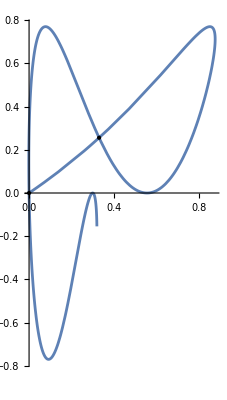

```mathematica
ParametricPlot[k[t],{t,0,5},Epilog->{PointSize[Large],Point[tocki]}]
```

### Subsection. naloga:

1. Definirajte funkcijo  g(x)=-x^3+8.
2. Narišite njen graf nad intervalom [-3,3] in ga shranite v spremenljivko graf1.
3. Izračunajte ničlo funkcije g (če želite samo realne ničle, funkciji Solve dodajte kot drugi parameter Reals).
4. Izračunajte ploščino lika, ki ga (v prvem kvadrantu) omejujeta koordinatni osi in graf te funkcije.
5. V spremenljivko  graf2 shranite graf funkcije nad intervalom, po katerem ste integrirali. Grafu dodajte določilo Filling→Axis.
6. Postavite oba grafa na isti koordinatni sistem s funkcijo Show.

```mathematica
g[x_]:=-x^3+8
```

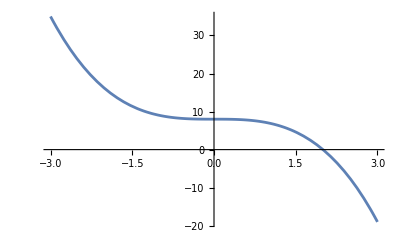

```mathematica
graf1 = Plot[g[x],{x,-3,3}]
```

```mathematica
t=First[x/.Solve[g[x]==0, Reals]]
```

2

```mathematica
Integrate[g[x],{x,0,t}]
```

12

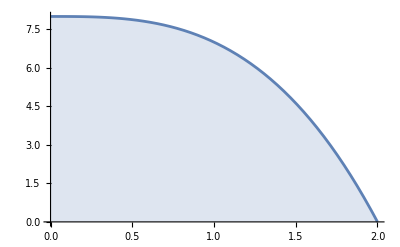

```mathematica
graf2=Plot[g[x],{x,0,t},Filling->Axis]
```

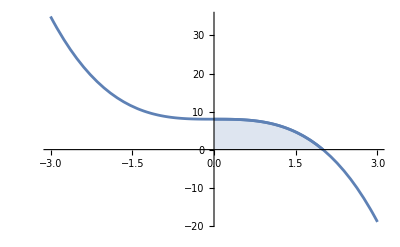

```mathematica
Show[graf1,graf2]
```

### Subsection. naloga:

1. Definiraj funkciji  s(x)=x^2-8  in  z(x)=x^2+10  ter nariši njuna grafa. Funkcija Plot bo narisala več grafov, če jih podate naštete v seznamu (v zavitih oklepajih, ločene z vejicami).
2. Poiščite njuni presečišči.
3. Izračunajte ploščino lika, ki ga omejujeta grafa teh dveh funkcij.
4. Še enkrat narišite grafa obeh funkcij, le da bo tokrat območje, katerega ploščino ste izračunali, pobarvano. Filling nastavite na {1→{2}} (kaj to naredi, poiščite v dokumentaciji nastavitve pod Applications).

```mathematica
s[x_]:=x^2-8
```

```mathematica
z[x_]:=-x^2+10
```

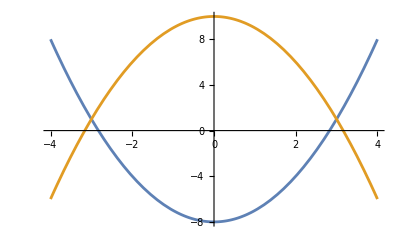

```mathematica
Plot[{s[x],z[x]},{x,-4,4}]
```

```mathematica
presecisci=x/.Solve[s[x] ==z[x]]
```

{-3,3}

```mathematica
Integrate[z[x]-s[x],{x,-3,3}]
```

72

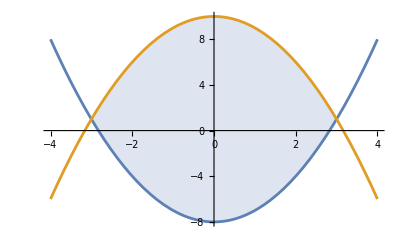

```mathematica
Plot[{s[x],z[x]},{x,-4,4},Filling->{1->{2}},FillingStyle->{Opacity[0.2],None}]
```

## Reševanje enačb

### Subsection. naloga:

1. Numerično izračunaj ničle polinoma  x^7-2 x^6-x^5-2 x^4+12 x^2-x+1. 
2. Preberite dokumentacijo funkcije NSolve in izračunajte samo realne ničle.

```mathematica
(* x^7-2x^6-x^5 - 2x^4 + 12x^2 - x + 1 *)
NSolve[x^7-2x^6-x^5-2x^4+12x^2-x+1]
```

{{x→-1.37527},{x→-0.356206-1.47367 ⅈ},{x→-0.356206+1.47367 ⅈ},{x→0.040941-0.283889 ⅈ},{x→0.040941+0.283889 ⅈ},{x→1.59494},{x→2.41086}}

```mathematica
NSolve[x^7-2x^6-x^5-2x^4+12x^2-x+1,Reals]
```

{{x→-1.37527},{x→1.59494},{x→2.41086}}

### Subsection. naloga:

Določi vsa realna števila, ki zadoščajo neenačbi  (|x-3|)/(x+1)>√(3-2x)

```mathematica
Reduce[(Abs[x-3])/(x+1)>(Sqrt[3-2x])]
```

-1<x<1||1<x≤3/2

### Subsection. naloga:

S funkcijo Solve rešujemo enačbe. Najbolj enostavno jo uporabimo, kadar imamo opravka z eno samo spremenljivko:
- Poiščite vsa kompleksna števila, ki zadoščajo enačbi  z̄=z^2. Za konjugiranje lahko uporabite *, funkcijo Conjugate ali pa znak Esc co Esc.
- Določite vrednost parametra a v enačbi (2a x+3a)/(3a + 5x)=(3a-4)/(3a - 5x), da bo  x=2  rešitev enačbe.

```mathematica
z/.Solve[Conjugate[z]==z^2]
```

{0,1,-1/2-(ⅈ √3)/2,-1/2+(ⅈ √3)/2}

```mathematica
x=2
```

```mathematica
Solve[(2a x+3a)/(3a+5x)==(3a-4)/(3a-5x)]
```

{{a→1/3 (11-√91)},{a→1/3 (11+√91)}}

### Subsection. naloga:

Rešujemo lahko tudi več enačb z več neznankami. V tem primeru enačbe naštejemo v zavite oklepaje (ločene naj bodo z vejicami).
Določite k in n tako, da bo šla premica y=k x+n skozi točki (-2,3) in (6,-1).

```mathematica
ClearAll[x,y,k,n]
```

```mathematica
Solve[{3==-2k+n, -1==6k+n}]
```

{{k→-1/2,n→2}}

### Subsection. naloga:

Sin je 3 leta starejši od hčere, mati pa je 23 let starejša od sina. Pred 6 leti je imela mati 4 krat toliko let kot sin in hči skupaj. Koliko je star vsak od njih? Napišite enačbe in jih rešite s pomočjo funkcije Solve.

```mathematica
ClearAll[sin,mati]
Solve[{sin==hci+3,mati==sin+23,mati-6==4(sin-6+hci-6)}]
```

{{hci→8,mati→34,sin→11}}

### Subsection. naloga:

Koliko začetnih členov zaporedja s splošnim členom  a_n=16-2n  moramo sešteti, da bo vsota enaka 36? Začnite s tem, da napišete vsoto ∑_(i=1)^k a_i, nato pa ustrezno enačbo.

```mathematica
Solve[Sum[16-2n,{n,1,k}]==36]
```

{{k→3},{k→12}}